## To Do & Notes

## Global Path Configue

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/shenjiaming/Desktop/Junior Courses/Network Project/compareFS_v0.1/NDN-EB-algo

## Read in Data

```mathematica
fileName = "exp-grid-delays-trace-10K.txt";
ipRate = 10000;
rawdata = Import[fileName];
data = StringSplit[rawdata,"\n"];
n = Length[data];
data2 = Table[StringSplit[row,"\t"],{row,data}];
head = data2⟦1⟧;
entries = data2⟦2;;n⟧;
Print["Head:"];
head
Print["Number of All Entries:"];
Length[entries]
Print["First Several Entries:"];
entries⟦1;;5⟧
```

Head:

{Time,Node,AppId,SeqNo,Type,DelayS,DelayUS,RetxCount,HopCount}

Number of All Entries:

5620

First Several Entries:

{{0.114816,0,258,0,LastDelay,0.114816,114816,1,4},{0.114816,0,258,0,FullDelay,0.114816,114816,1,4},{0.123296,0,258,1,LastDelay,0.123196,123196,1,4},{0.123296,0,258,1,FullDelay,0.123196,123196,1,4},{0.131776,0,258,2,LastDelay,0.131576,131576,1,4}}

## Data Preprocessing

```mathematica
(*选择需要分析的Entires*)
consumerEntries = Select[entries,StringMatchQ[#⟦2⟧,"0"]&&StringMatchQ[#⟦5⟧,"FullDelay"] &];
Print["Number of Sample Entries:"];
n = Length[consumerEntries]
```

Number of Sample Entries:

2810

```mathematica
Dynamic[ele]
recTime = Table[Interpreter["Number"][ele⟦1⟧],{ele,consumerEntries}];
seqNo = Table[Interpreter["Number"][ele⟦4⟧],{ele,consumerEntries}];
delayS = Table[Interpreter["Number"][ele⟦6⟧],{ele,consumerEntries}];
retxCount = Table[Interpreter["Number"][ele⟦8⟧],{ele,consumerEntries}];
hopCount = Table[Interpreter["Number"][ele⟦9⟧],{ele,consumerEntries}];
```

## Basic Analysis

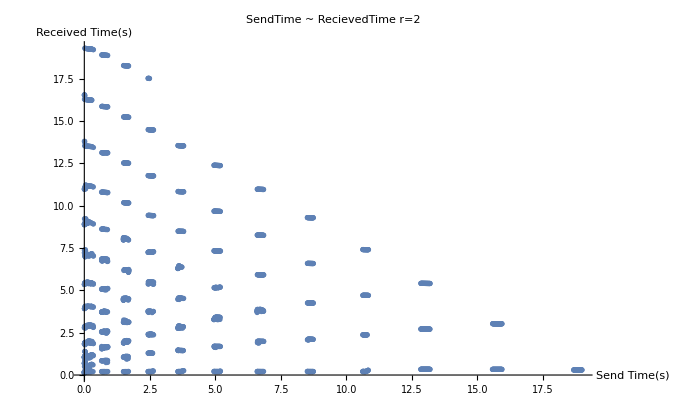

```mathematica
sendTime = Table[recTime⟦i⟧-delayS⟦i⟧,{i,n}];
sendTime2delayS = Table[{sendTime⟦i⟧,delayS⟦i⟧},{i,n}];
ListPlot[
sendTime2delayS,
PlotLabel ->  "SendTime ~ RecievedTime r=2",
AxesLabel-> {"Send Time(s)","Received Time(s)"},
(*PlotRange->{{0,5},{0,5}},*)
PlotStyle->Thin
]
```

```mathematica
Mean[
Table[
delayS⟦id⟧,
{id,Select[Range[1,n],sendTime⟦#⟧>10&]}
]
]
```

2.50631

```mathematica
N[Mean[retxCount]]
```

4.98793

reqTime

## Visualization

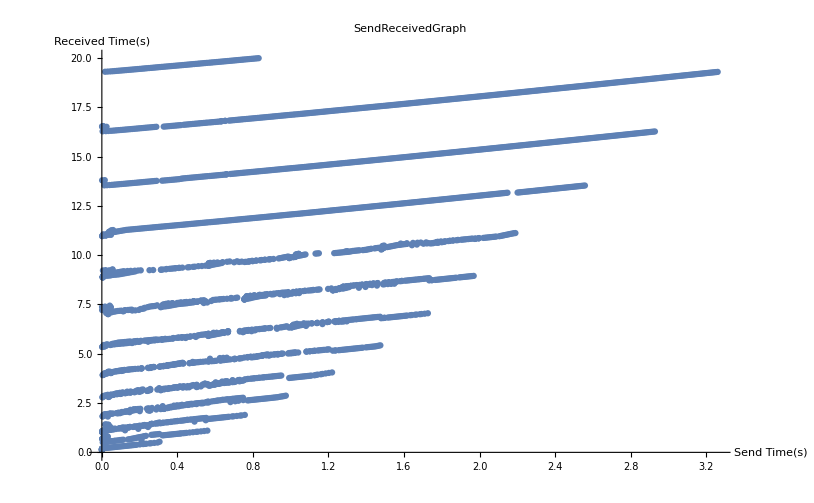

```mathematica
(*每秒传10W个interest packet，所以除以interest packet rate*)
seqNo2recTime = Table[{seqNo⟦i⟧/ipRate,recTime⟦i⟧},{i,n}];
ListPlot[seqNo2recTime,
PlotLabel ->  "SendReceivedGraph",
AxesLabel-> {"Send Time(s)","Received Time(s)"},
(*PlotRange->{{0,5},{0,5}},*)
PlotStyle->Thin
]
```

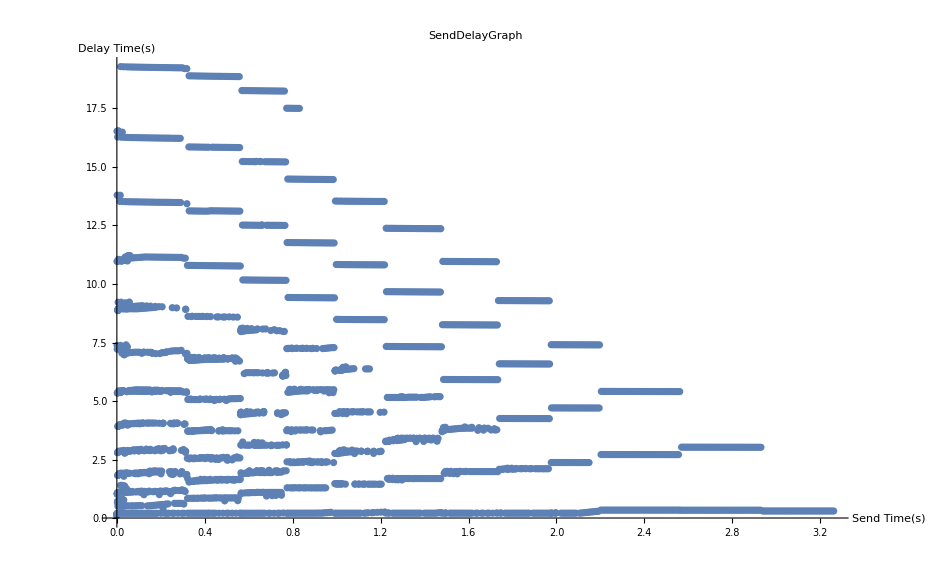

```mathematica
secNo2delayS = Table[{seqNo⟦i⟧/ipRate,delayS⟦i⟧},{i,n}];
ListPlot[secNo2delayS,
PlotLabel ->  "SendDelayGraph",
AxesLabel-> {"Send Time(s)","Delay Time(s)"},
PlotStyle->Thin
]
```

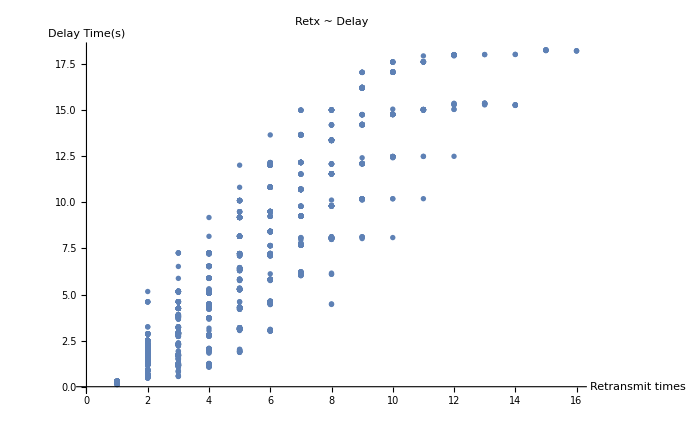

```mathematica
retxCount2delayS = Table[{retxCount⟦i⟧,delayS⟦i⟧},{i,n}];
ListPlot[retxCount2delayS,
PlotLabel ->  "Retx ~ Delay",
AxesLabel-> {Style["Retransmit times",14],Style["Delay Time(s)",14]},
PlotStyle->Thin
]
```

```mathematica
retxCount2delayS = Table[{recTime⟦i⟧,delayS⟦i⟧,retxCount⟦i⟧},{i,n}];
ListPointPlot3D[retxCount2delayS,
PlotLabel ->  "ReceivedDelayRetransmitGraph",
AxesLabel-> {"Received Times(s)","Delay Time(s)","Retransmit times"},
PlotStyle->Thin
]
```

-Graphics3D-

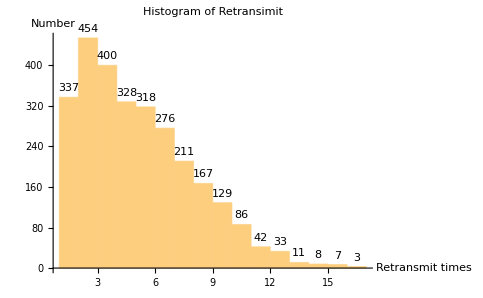

```mathematica
Histogram[retxCount,
ChartLayout->"Stacked",
PlotLabel->Style["Histogram of Retransimit","Title",14],
LabelingFunction->Above,
AxesLabel->{"Retransmit times","Number"}
]
```

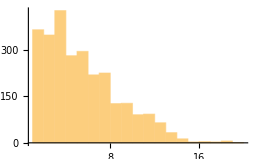
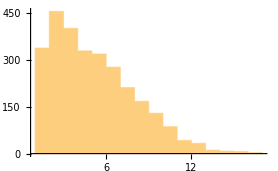
```mathematica
{-Graphics--Graphics-}-> {"Fixed","Exp"}
```

{-Graphics- -Graphics-}→{Fixed,Exp}

## Tmp

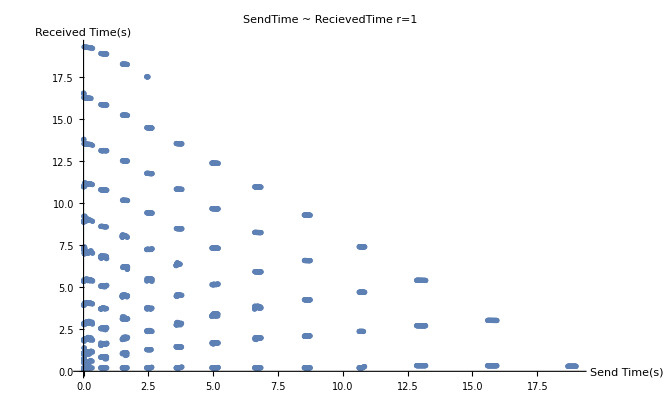
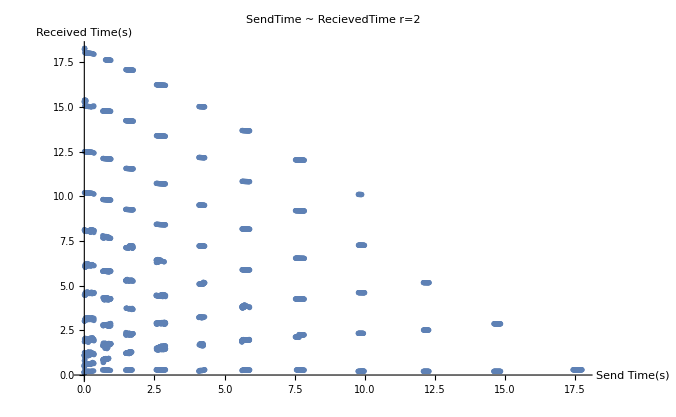
```mathematica
g1=
-Graphics-
g2=
-Graphics-
```

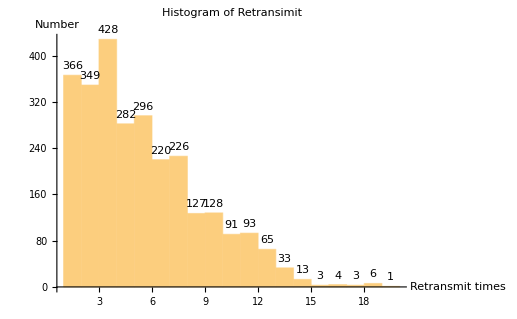
```mathematica
g3=
-Graphics-
```

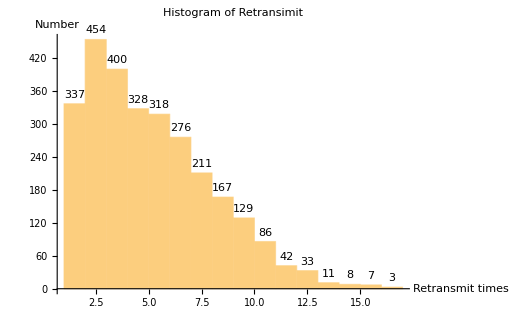
```mathematica
g4=
-Graphics-
```

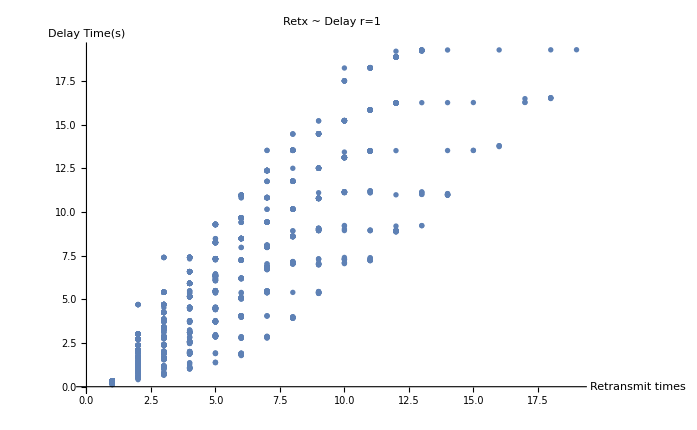
```mathematica
g5=-Graphics-
```

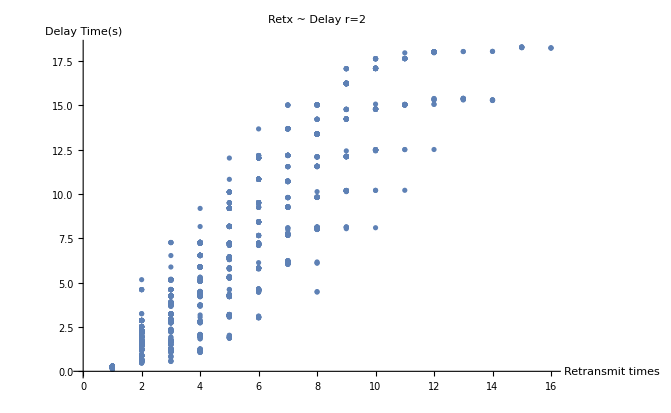
```mathematica
g6= 
-Graphics-
```